# Nanobot Theory : Data Analysis and Plotting

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
baseDirectory=NotebookDirectory[];
```

```mathematica
scaleFac = 1.0;(* Scaling Factor for dipole coordinates *)
oldstructure=1/scaleFac Import[baseDirectory<>"/data_Au@Ag_Octahedra/octahedra_core.csv"];
newstructure=1/scaleFac Import[baseDirectory<>"/data_Au@Ag_Octahedra/octahedra_overall.csv"];
```

```mathematica
Dimensions/@{oldstructure,newstructure}
```

{{3303,3},{4089,3}}

```mathematica
npImage = Graphics3D[{{Yellow,Opacity[0.5],Sphere[oldstructure,1/2]},{Blue,Opacity[0.4],Sphere[Complement[newstructure,oldstructure],1/2]}},Boxed->True,ViewProjection->"Orthographic",ViewPoint->{2,-2,1},ImageSize->{300,300}]
```

-Graphics3D-

```mathematica
Export[baseDirectory<>"np_image.png",npImage,ImageResolution-> 300]
```

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Au@Ag octahedra\np_image.png

```mathematica
dipoleLength=Quantity[1.0,"nm"];
```

```mathematica
d=QuantityMagnitude[10^-3 dipoleLength]; (* For plotting 10^-3 is a scaling factor *)
```

```mathematica
(*deleteIndex = 1+Flatten@IntegerPart@N@Import[baseDirectory<>"/data_Au@Ag_Octahedra/exp1/from_edge_delete_sequence.csv"];
deleteIndex=Table[{i},{i,deleteIndex}];
data=Import[baseDirectory<>"//data_Au@Ag_Octahedra/exp1/data_random_from_edge_seed_100.csv"];*)
deleteIndex = 1+Flatten@IntegerPart@N@Import[baseDirectory<>"/data_Au@Ag_Octahedra/exp1/from_center_delete_sequence.csv"];
deleteIndex=Table[{i},{i,deleteIndex}];
data=Import[baseDirectory<>"//data_Au@Ag_Octahedra/exp1/data_random_from_center_seed_100.csv"];
```

```mathematica
wavelength = Table[0.39+0.01*i,{i,51}];
```

```mathematica
plotUVVis[index_]:= Block[{Au,structure,reffi,tempData,intp,plot1,plot2,fig},
Au=Delete[newstructure,deleteIndex⟦;;index⟧];
structure=Graphics3D[{{Yellow,Opacity[0.5],Sphere[oldstructure,1/2]},{Blue,Opacity[0.4],Sphere[Complement[Au,oldstructure],1/2]}},Boxed->False,ViewProjection->"Orthographic",ViewPoint->{2,-2,1},ImageSize->{300,300}];
reffi=(3/(4π)d^3 Length@Au )^(1/3);
tempData=Transpose[{1000*wavelength,data⟦All,1+index⟧/(π reffi^2)}];
intp=Interpolation[tempData,InterpolationOrder->2];
plot1=Plot[intp[x],{x,400,650},PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange->{0,12}];
plot2=ListPlot[tempData,PlotStyle->{Black,PointSize[0.02]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}];
fig=Show[{plot1,plot2},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},AspectRatio->1,ImageSize->300,PlotRange->{0,1.8}];{structure,fig}]
```

```mathematica
DataUVVis[index_]:= Block[{Au,structure,reffi,tempData,intp,plot1,plot2,fig},
Au=Delete[newstructure,deleteIndex⟦;;index⟧];
reffi=(3/(4π)d^3 Length@Au )^(1/3);
tempData=Transpose[{1000*wavelength,data⟦All,1+index⟧/(π reffi^2)}];Return[data⟦All,1+index⟧/(π reffi^2)]]
```

```mathematica
dataAll = Table[DataUVVis[i],{i,786,0,-1}];
```

```mathematica
sampled = Table[0+1/786*(i-1),{i,1,787}];
```

```mathematica
c = Reverse@Table[ColorData["Rainbow"][i],{i,0,1,1/5}]
```

{RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.471412, 0.108766, 0.527016]}

```mathematica
p1=PDF[NormalDistribution[0.2,0.08]][sampled]/Total[PDF[NormalDistribution[0.2,0.08]][sampled]];
p2=PDF[NormalDistribution[0.2,0.2]][sampled]/Total[PDF[NormalDistribution[0.2,0.2]][sampled]];
p3 =PDF[NormalDistribution[0.50,0.08]][sampled]/Total[PDF[NormalDistribution[0.50,0.08]][sampled]];
p4 =PDF[NormalDistribution[0.50,0.2]][sampled]/Total[PDF[NormalDistribution[0.50,0.2]][sampled]];
p5 =PDF[NormalDistribution[0.8,0.08]][sampled]/Total[PDF[NormalDistribution[0.8,0.08]][sampled]];
p6 =PDF[NormalDistribution[0.8,0.2]][sampled]/Total[PDF[NormalDistribution[0.8,0.2]][sampled]];
```

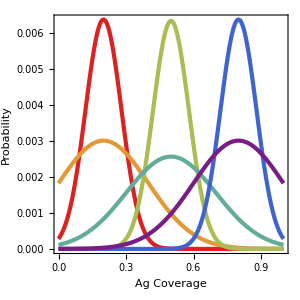

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Au@Ag octahedra\/Distribution.png

```mathematica
f1 = ListLinePlot[{Transpose[{sampled,p1}],Transpose[{sampled,p2}],Transpose[{sampled,p3}],Transpose[{sampled,p4}],Transpose[{sampled,p5}],Transpose[{sampled,p6}]},LabelStyle->{Directive[Black,FontColor->Black,FontSize->14]},Frame-> True,PlotStyle->Table[{i,Thickness[0.010]},{i,c}],FrameStyle->Directive[16,FontColor->Black],FrameLabel->{"Ag Coverage","Probability"},AspectRatio->1,ImageSize->300,PlotRange->All]
Export[baseDirectory<>"/Distribution.png",f1,ImageResolution-> 300]
```

```mathematica
c = Reverse@Table[ColorData["Rainbow"][i],{i,0,1,1/5}];
dataP = {Total[(dataAll*p1)],Total[(dataAll*p2)],Total[(dataAll*p3)],Total[(dataAll*p4)],Total[(dataAll*p5)],Total[(dataAll*p6)]};
```

```mathematica
Table[Position[Abs[sampled-i],Min[Abs[sampled-i]]],{i,{0.2,0.5,0.8}}]
Table[Min[Abs[sampled-i]],{i,{0.2,0.5,0.8}}]
```

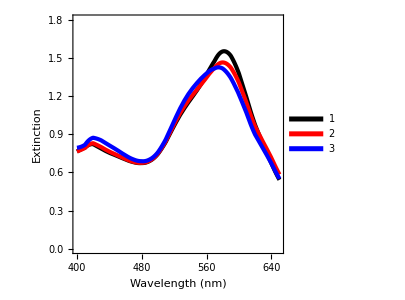

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Au@Ag octahedra\/Distribution1.png

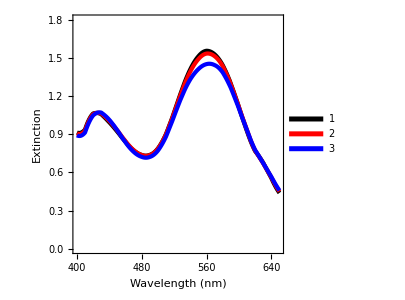

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Au@Ag octahedra\/Distribution2.png

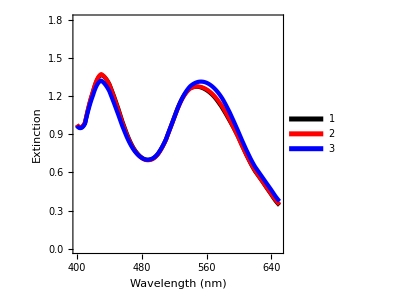

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Au@Ag octahedra\/Distribution3.png

```mathematica
tempData1=Transpose[{1000*wavelength,dataP⟦1⟧}];
tempData2=Transpose[{1000*wavelength,dataP⟦2⟧}];
tempData3=Transpose[{1000*wavelength,dataAll⟦158⟧}];
intp1=Interpolation[tempData1,InterpolationOrder->2];
intp2=Interpolation[tempData2,InterpolationOrder->2];
intp3=Interpolation[tempData3,InterpolationOrder->2];
plot1=Plot[{intp3[x],intp1[x],intp2[x]},{x,400,650},PlotStyle->{{Black,Thickness[0.010]},{Red,Thickness[0.010]},{Blue,Thickness[0.010]}},FrameStyle->Directive[16,FontColor->Black],PlotRange->{0,1.8},AspectRatio->1,ImageSize->300,Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},PlotLegends->Placed[{"1","2","3"},{0.15,0.8}]]
Export[baseDirectory<>"/Distribution1.png",plot1,ImageResolution-> 300] 

tempData1=Transpose[{1000*wavelength,dataP⟦3⟧}];
tempData2=Transpose[{1000*wavelength,dataP⟦4⟧}];
tempData3=Transpose[{1000*wavelength,dataAll⟦394⟧}];
intp1=Interpolation[tempData1,InterpolationOrder->2];
intp2=Interpolation[tempData2,InterpolationOrder->2];
intp3=Interpolation[tempData3,InterpolationOrder->2];
plot1=Plot[{intp3[x],intp1[x],intp2[x]},{x,400,650},PlotStyle->{{Black,Thickness[0.010]},{Red,Thickness[0.010]},{Blue,Thickness[0.010]}},FrameStyle->Directive[16,FontColor->Black],PlotRange->{0,1.8},AspectRatio->1,ImageSize->300,Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},PlotLegends->Placed[{"1","2","3"},{0.15,0.8}]]
Export[baseDirectory<>"/Distribution2.png",plot1,ImageResolution-> 300] 

tempData1=Transpose[{1000*wavelength,dataP⟦5⟧}];
tempData2=Transpose[{1000*wavelength,dataP⟦6⟧}];
tempData3=Transpose[{1000*wavelength,dataAll⟦630⟧}];
intp1=Interpolation[tempData1,InterpolationOrder->2];
intp2=Interpolation[tempData2,InterpolationOrder->2];
intp3=Interpolation[tempData3,InterpolationOrder->2];
plot1=Plot[{intp3[x],intp1[x],intp2[x]},{x,400,650},PlotStyle->{{Black,Thickness[0.010]},{Red,Thickness[0.010]},{Blue,Thickness[0.010]}},FrameStyle->Directive[16,FontColor->Black],PlotRange->{0,1.8},AspectRatio->1,ImageSize->300,Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},PlotLegends->Placed[{"1","2","3"},{0.8,0.8}]]
Export[baseDirectory<>"/Distribution3.png",plot1,ImageResolution-> 300]
```